```mathematica
r2Exact[λ_]:= 1/(A-B)^4((8 A^2 B^2 (b^2+e^2)+4 A B (-A B (b-e)^2+(b+e) p2) λ^2+p2^2 λ^4)/((f+ λ^2)^2) + (4 A B (b-e) √(1-λ^2) (2 A B (b+e)+p2 λ^2))/((f+λ^2)^2))
```

```mathematica
NUM1[s_]:=8 A^2 B^2 (b^2+e^2)+4 A B (-A B (b-e)^2+(b+e) p2) s+p2^2 s^2
NUM2[s_]:= 4 A B (b-e) (2 A B (b+e)+p2 s)
r2ExactS[s_]:= 1/(A-B)^4(NUM1[s]/(f+ s)^2 + (NUM2[s] √(1-s))/(f+s)^2)

H1[s_]:= -s/f NUM1[s]
H2[s_]:= -s/f NUM2[s]
Trialr2ExactS[s_]:= 1/(A-B)^4(H1[-f]/(f+ s)^2 + (H2[-f] √(1-s))/(f+s)^2)
```

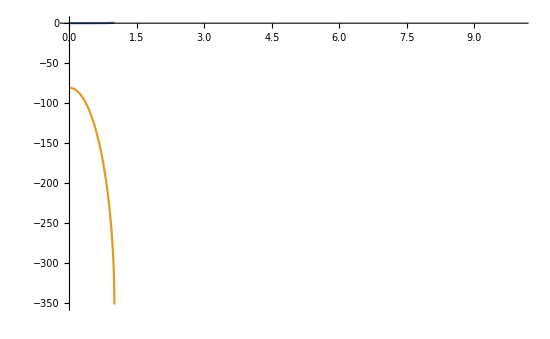

```mathematica
Plot[{r2Exact[λ],Trialr2ExactS[λ^2]-51500},{λ,0,10}]
```

```mathematica
Apart[(8 A^2 B^2 (b^2+e^2)+4 A B (-A B (b-e)^2+(b+e) ( b*A^2+e*B^2-(e+b)*A*B)) x+( b*A^2+e*B^2-(e+b)*A*B)^2 x^2)/(f+x)^2]
```

(A-B)^2 (A b-B e)^2+1/(f+x)^2(8 A^2 b^2 B^2+8 A^2 B^2 e^2-4 A^3 b^2 B f+8 A^2 b^2 B^2 f-4 A^3 b B e f-4 A b B^3 e f+8 A^2 B^2 e^2 f-4 A B^3 e^2 f+A^4 b^2 f^2-2 A^3 b^2 B f^2+A^2 b^2 B^2 f^2-2 A^3 b B e f^2+4 A^2 b B^2 e f^2-2 A b B^3 e f^2+A^2 B^2 e^2 f^2-2 A B^3 e^2 f^2+B^4 e^2 f^2)-1/(f+x)2 (-2 A^3 b^2 B+4 A^2 b^2 B^2-2 A^3 b B e-2 A b B^3 e+4 A^2 B^2 e^2-2 A B^3 e^2+A^4 b^2 f-2 A^3 b^2 B f+A^2 b^2 B^2 f-2 A^3 b B e f+4 A^2 b B^2 e f-2 A b B^3 e f+A^2 B^2 e^2 f-2 A B^3 e^2 f+B^4 e^2 f)

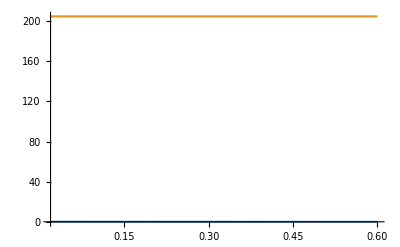

```mathematica
TT[r_]:= 1/(Sqrt[J A B](A-B)^4)(ψ((k ArcTanh[(f k^2+( xSUB[r]) (k^2 ( xSUB[r])+I k √(1-k^2 ( xSUB[r])^2)))/(√f k √(1+f k^2))])/(√f √(-k^2) √(1+f k^2)))+ (χ-f ψ)(((√f ( xSUB[r]) √(1-k^2 ( xSUB[r])^2))/((1+f k^2) (f+( xSUB[r])^2))+((k+2 f k^3) ArcTanh[(f k^2+( xSUB[r]) (k^2 ( xSUB[r])+I k √(1-k^2 ( xSUB[r])^2)))/(√f k √(1+f k^2))])/(I k (1+f k^2)^(3/2)))/(2 f^(3/2))))
Plot[{Re[TT[r]],Im[TT[r]]},{r,b,0.6}]
```

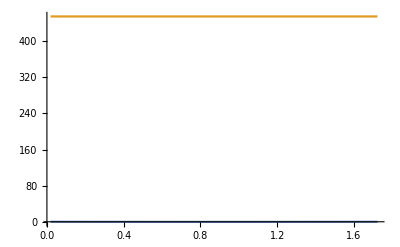

```mathematica
TT
```

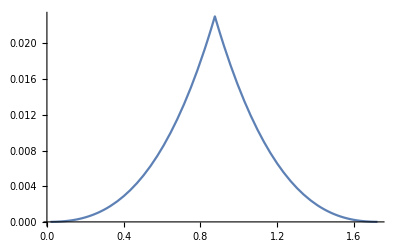

```mathematica
FullTT[r_]:= 1/(Sqrt[J A B](A-B)^4)( p2^2 EllipticF[ArcSin[( xSUB[r])],k^2]+(Þ-2 f p2^2)EllipticPi[-1/f,ArcSin[( xSUB[r])],k^2]/f + (ð+(f^2 p2^2-Þ f))(1/(2 f^2 (1+f) k (1+f k^2) (f+( xSUB[r])^2))(f k ( xSUB[r]) √(1-( xSUB[r])^2) √(1-k^2 ( xSUB[r])^2)+(f+( xSUB[r])^2) (f k^2 (-EllipticE[- ArcSin[k ( xSUB[r])],1/k^2]+(1+f) EllipticF[- ArcSin[k ( xSUB[r])],1/k^2])-(1+2 f+f (2+3 f) k^2) EllipticPi[-1/(f k^2),- ArcSin[k ( xSUB[r])],1/k^2])))
+ ψ((k ArcTanh[(f k^2+( xSUB[r]) (k^2 ( xSUB[r])+I k √(1-k^2 ( xSUB[r])^2)))/(√f k √(1+f k^2))])/(√f √(-k^2) √(1+f k^2)))+ (χ-f ψ)(((√f ( xSUB[r]) √(1-k^2 ( xSUB[r])^2))/((1+f k^2) (f+( xSUB[r])^2))+((k+2 f k^3) ArcTanh[(f k^2+( xSUB[r]) (k^2 ( xSUB[r])+I k √(1-k^2 ( xSUB[r])^2)))/(√f k √(1+f k^2))])/(I k (1+f k^2)^(3/2)))/(2 f^(3/2))))
Plot[Re[FullTT[r]],{r,b,e}]
```

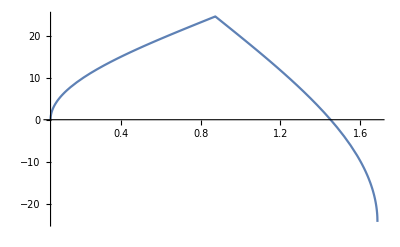

```mathematica
HJ[r_]:= - ArcSin[k ( xSUB[r])]
HJ2[r_]:=(ð+(f^2 p2^2-Þ f))1/(2 f^2 (1+f) k (1+f k^2) (f+( xSUB[r])^2))(f k ( xSUB[r]) √(1-( xSUB[r])^2) √(1-k^2 ( xSUB[r])^2)+(f+( xSUB[r])^2) (f k^2 (-EllipticE[-π/2+ ArcTan[Sqrt[HYP[r]^2-k^2 OPP[r]^2]/(k OPP[r])],1/k^2]+(1+f)k EllipticF[-(π/2- ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2])-(1+2 f+f (2+3 f) k^2) EllipticPi[-1/(f k^2),-π/2+ ArcTan[Sqrt[HYP[r]^2-k^2 OPP[r]^2]/(k OPP[r])],1/k^2]))
Plot[{HJ2[r]},{r,b,e}]
```

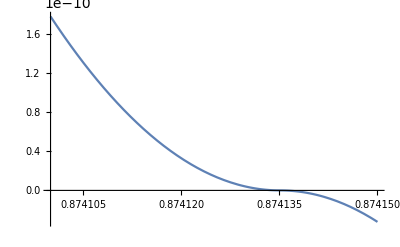

```mathematica
MIDFUNCT1[r_]:=-EllipticE[- ArcSin[k(xSUB[r])],1/k^2]
MIDFUNCT2[r_]:=(-(EllipticE[- ArcSin[(xSUB[r])],k^2]- (1-k^2)EllipticF[- ArcSin[(xSUB[r])],k^2]))/k
Plot[Re[MIDFUNCT2'[r]],{r,0.87410,0.87415},PlotRange->All]
Plot[{MIDFUNCT1[r],MIDFUNCT2[r], MIDFUNCT1[r]-MIDFUNCT2[r]},{r,b,e},PlotRange->All]
```

```mathematica
MIDFUNCT1[0.6`50]-MIDFUNCT2[0.6`50]
```

0.

```mathematica
MIDFUNCT1[0.8`50]-MIDFUNCT2[0.8`50]
```

0.

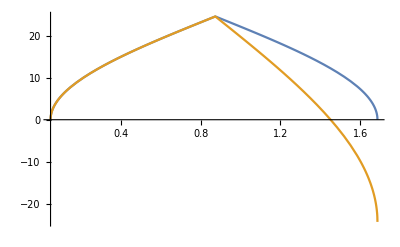

```mathematica
HJ1[r_]:=(ð+(f^2 p2^2-Þ f))1/(2 f^2 (1+f) k (1+f k^2) (f+(xSUB[r])^2))(f k (xSUB[r]) √(1-(xSUB[r])^2) √(1-k^2 (xSUB[r])^2)+(f+(xSUB[r])^2) (f k^2 (-EllipticE[- ArcSin[k(xSUB[r])],1/k^2]+(1+f) EllipticF[- ArcSin[k (xSUB[r])],1/k^2])-(1+2 f+f (2+3 f) k^2) EllipticPi[-1/(f k^2),- ArcSin[k (xSUB[r])],1/k^2]))


HJ2[r_]:= (ð+(f^2 p2^2-Þ f))1/(2 f^2 (1+f) k (1+f k^2) (f+(xSUB[r])^2))(f k (xSUB[r]) √(1-(xSUB[r])^2) √(1-k^2 (xSUB[r])^2)+(f+(xSUB[r])^2) (f k^2 (-EllipticE[- ArcSin[k(xSUB[r])],1/k^2]+(1+f) k^2 EllipticF[-1/k(π/2- ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2])-(1+2 f+f (2+3 f) k^2) EllipticPi[-1/(f k^2),- ArcSin[k (xSUB[r])],1/k^2]))
Plot[{HJ1[r],HJ2[r]},{r,b,e}]
```

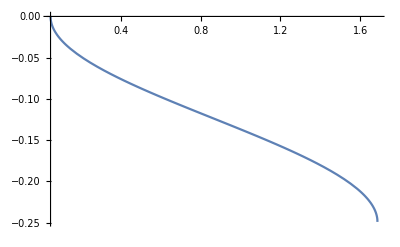

-0.08697945390190753456174591233364395532961149777

-0.08697945390190753456174591233364395532961149777

-0.08697945390190753456174591233364395532961149777

0.

0.

```mathematica
HJ2[r_]:=   EllipticF[- ArcSin[k(xSUB[r])],1/k^2]

HJ3[r_]:=   k EllipticF[-ArcSin[xSUB[r]],k^2]


HJ4[r_]:=   k EllipticF[-(π/2- ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]

Plot[{HJ4[r]},{r,b,e},PlotRange->All,WorkingPrecision->50]

HJ2[0.5`50]
HJ3[0.5`50]
HJ4[0.5`50]
HJ2[0.5`50]-HJ3[0.5`50]
HJ3[0.5`50]-HJ4[0.5`50]
```

```mathematica
HJ2[0.5`50]-HJ3[0.5`50]
```

0.000049799042675975049821680450285202356274665

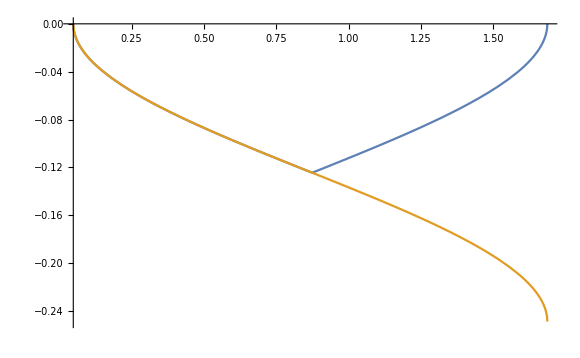

```mathematica
HJ2[r_]:=   EllipticPi[-1/(f k^2),- ArcSin[k (xSUB[r])],1/k^2]

HJ3[r_]:=k EllipticPi[-k^2/f,-(π/2- ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]


HJ4[r_]:= EllipticPi[-1/(f k^2),- ArcSin[k (xSUB[r])],1/k^2]

Plot[{HJ2[r],HJ3[r]},{r,b,e},PlotRange->All]
```

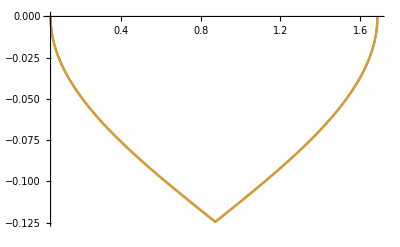

-0.086977671073293513866822297282904987333488804

-0.086977671073293513866822297282904987333488804

-0.086977671073293513866822297282904987333488804

0.

0.

```mathematica
HJ2[r_]:=   EllipticPi[-1/(f k^2),- ArcSin[k (xSUB[r])],1/k^2]

HJ3[r_]:= k EllipticPi[-1/f,- ArcSin[(xSUB[r])],k^2]

HJ4[r_]:= k EllipticPi[-1/f,- (π/2- ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]


Plot[{HJ2[r],HJ3[r]},{r,b,e}]
HJ2[0.5`50]
HJ3[0.5`50]
HJ4[0.5`50]
HJ2[0.5`50]-HJ3[0.5`50]
HJ3[0.5`50]-HJ4[0.5`50]
```

```mathematica
FullSimplify[  EllipticF[- ArcSin[l ϕ],1/l^2]]
```

-EllipticF[ArcSin[l ϕ],1/l^2]

```mathematica
Clear[A,B,e,b]
```

```mathematica
Together[1-(4A B(e-r)(r-b))/(B(e-r)+A(r-b))^2]
```

```mathematica
FullSimplify[(A^2 b^2+2 A b B e+B^2 e^2-2 A^2 b r-2 A b B r-2 A B e r-2 B^2 e r+A^2 r^2+2 A B r^2+B^2 r^2)/(-A b+B e+A r-B r)^2]
```

```mathematica
Sqrt[(A b+B e-(A+B) r)^2/(A (b-r)+B (-e+r))^2]
```

```mathematica
FullSimplify[√((A b+B e-(A+B) r)^2/(A (b-r)+B (-e+r))^2)]
```

```mathematica
(A (b-r)+B( e-r))/(A (b-r)+B (-e+r))
```

(A (b-r)+B (e-r))/(A (b-r)+B (-e+r))

```mathematica
Simplify[(-A b+B e+A r-B r-2 √(A B) √((e-r) (-b+r)))/(-A b+B e+A r-B r)]
```

(A (b-r)+B (-e+r)+2 √(A B) √((b-r) (-e+r)))/(A (b-r)+B (-e+r))

Plot::precw: The precision of the argument function ((10.2087613919797037666275899794177746661292508167 (-0.048893755848217133160647973133115435718418197931+r)-«80» («97»-r))/(10.2087613919797037666275899794177746661292508167 (0.048893755848217133160647973133115435718418197931-r)+«80» (-«97»+r))-√(1-(«1»)^2)) is less than WorkingPrecision (50.).

Plot::precw: The precision of the argument function ({(10.2087613919797037666275899794177746661292508167 (0.048893755848217133160647973133115435718418197931-r)+10.3746429952895694157925802386326647941865052827 (-1.68618149879521115355930651647423539540724888593+r))-0}) is less than WorkingPrecision (50.).

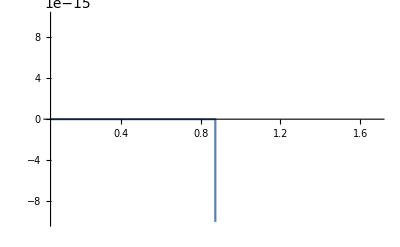

```mathematica
Plot[(A (-b+r)-B( e-r))/(A (b-r)+B (-e+r))- Sqrt[1-(xSUB[r])^2],{r,b,e}, PlotRange->{{b,e},{-0.00000000000001,0.00000000000001}},WorkingPrecision->50]
```

```mathematica
chn[r_]:=(A (-b+r)-B( e-r))/(A (b-r)+B (-e+r))- Sqrt[1-(xSUB[r])^2]

chn[0.4`50]
```

0.

```mathematica
TestTT[r_]:= 1/(ϡ Sqrt[J A B]) (α(EllipticF[(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),KZ2])+( β-(α ϛ)/ϡ)(1/(D1^2-D2^2)(-EllipticPi[1/D1^2,ArcSin[(xSUB[r])],k^2]+EllipticPi[1/D2^2,ArcSin[(xSUB[r])],k^2]))+(φ-(ϟ α)/ϡ)((-D2^2 EllipticPi[1/D1^2,ArcSin[(xSUB[r])],k^2]+D1^2 EllipticPi[1/D2^2,ArcSin[(xSUB[r])],k^2])/(D1^4 D2^2-D1^2 D2^4))+γ ((k (-D1 √(-1+D1^2 k^2) (-1+D2^2 k^2) ArcTanh[(D1^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D1 k √(-1+D1^2 k^2))]+D2 (-1+D1^2 k^2) √(-1+D2^2 k^2) ArcTanh[(D2^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D2 k √(-1+D2^2 k^2))]))/((D1-D2) (D1+D2) √(-k^2) (-1+D1 k) (1+D1 k) (-1+D2 k) (1+D2 k)))+  ω (1/((D1^2-D2^2) k)√(-k^2) (ArcTanh[(D1^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D1 k √(-1+D1^2 k^2))]/(D1 √(-1+D1^2 k^2))-ArcTanh[(D2^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D2 k √(-1+D2^2 k^2))]/(D2 √(-1+D2^2 k^2)))));
Plot[Re[TestTT[r]],{r,chi-0.1,chi+0.1},PlotRange->All,WorkingPrecision->50]
```

-Graphics-

-Graphics-

```mathematica
UNITTestTT[r_]:= 1/(ϡ Sqrt[J A B]) (( β-(α ϛ)/ϡ)(1/(D1^2-D2^2)(-EllipticPi[1/D1^2,ArcSin[(xSUB[r])],k^2]+EllipticPi[1/D2^2,ArcSin[(xSUB[r])],k^2]))+(φ-(ϟ α)/ϡ)((-D2^2 EllipticPi[1/D1^2,ArcSin[(xSUB[r])],k^2]+D1^2 EllipticPi[1/D2^2,ArcSin[(xSUB[r])],k^2])/(D1^4 D2^2-D1^2 D2^4)));
UNITTestTT2[r_]:= 1/(ϡ Sqrt[J A B]) (( β-(α ϛ)/ϡ)(1/(D1^2-D2^2)(-EllipticPi[1/D1^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]+EllipticPi[1/D2^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]))+(φ-(ϟ α)/ϡ)((-D2^2 EllipticPi[1/D1^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]+D1^2 EllipticPi[1/D2^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2])/(D1^4 D2^2-D1^2 D2^4)));
Plot[Re[UNITTestTT[r]]- Re[UNITTestTT2[r]],{r,chi-0.000000001,chi+0.000000001},PlotRange->All,WorkingPrecision->50]
```

-Graphics-

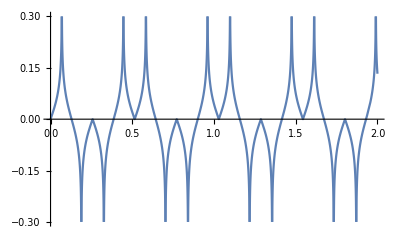

```mathematica
RPINTTEST[r_] := 1/(ϡP Sqrt[J A B]) (( βP-(αP ϛP)/ϡP)(1/(D1P^2-D2P^2)(-EllipticPi[1/D1P^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]+EllipticPi[1/D2P^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]))+(φP-(ϟP αP)/ϡP)((-D2P^2 EllipticPi[1/D1P^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]+D1P^2 EllipticPi[1/D2P^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2])/(D1P^4 D2P^2-D1P^2 D2P^4)));
Plot[Re[RPINTTEST[r[λ]]],{λ,0,2},PlotRange->{{0,2},{-0.3,0.3}}]
```

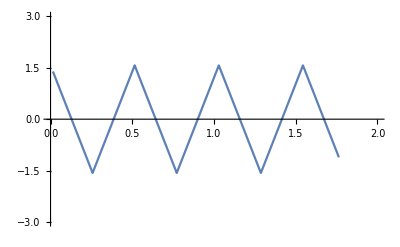

```mathematica
RPINTTEST[r_] :=
ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]
Plot[Re[RPINTTEST[r[λ]]],{λ,b,e},PlotRange->{{0,2},{-3,3}}]
```

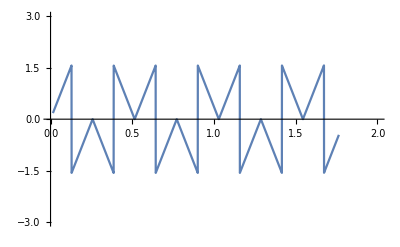

```mathematica
Plot[Re[RPINTTEST[r[λ]]],{λ,b,e},PlotRange->{{0,2},{-3,3}}]
```

```mathematica
Series[RPINTTEST[r[λ]],{λ,0.2,10}]
```

SeriesData::ssdn: Attempt to evaluate a series at the number 0.0000408571. Returning Indeterminate.

SeriesData::ssdn: Attempt to evaluate a series at the number 0.0408572. Returning Indeterminate.

SeriesData::ssdn: Attempt to evaluate a series at the number 0.0816735. Returning Indeterminate.

General::stop: Further output of SeriesData::ssdn will be suppressed during this calculation.

-Graphics-

(2 (3381.3-3325.88 JacobiCN[12.2086 λ,0.000376944])+33.7655 JacobiSN[12.2086 λ,0.000376944]^2)/(7604.56+0.19395 JacobiSN[12.2086 λ,0.000376944]^2)

-Graphics-

```mathematica
(√(A B) (b-e) JacobiCN[√(A B J) λ,k^2] (-A-B+(A-B) JacobiCN[√(A B J) λ,k^2]))/(√(-(A B (b-e)^2 (-1+JacobiCN[√(A B J) λ,k^2]^2))/((A+B+(A-B) JacobiCN[√(A B J) λ,k^2])^2)) (4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))
```

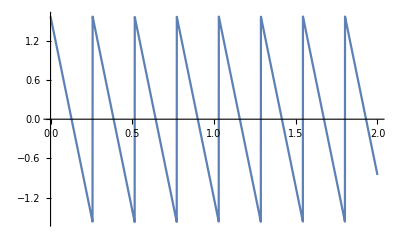

```mathematica
Test[r_] := ArcTan[((b-e) JacobiCN[√(A B J) λ,k^2] (-A-B+(A-B) JacobiCN[√(A B J) λ,k^2])Sqrt[(A+B+(A-B) JacobiCN[√(A B J) λ,k^2])^2])/((e-b)(JacobiSN[√(A B J) λ,k^2]) (4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))];
Plot[Test[λ],{λ,0,2}]
```

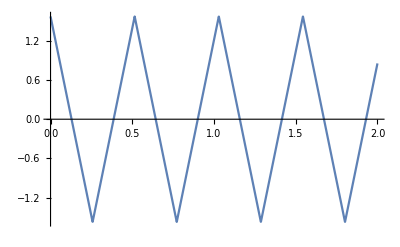

-Graphics-

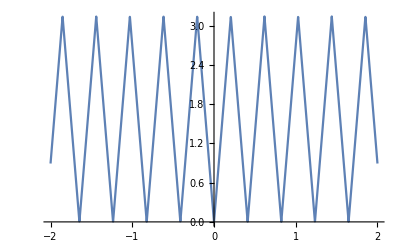

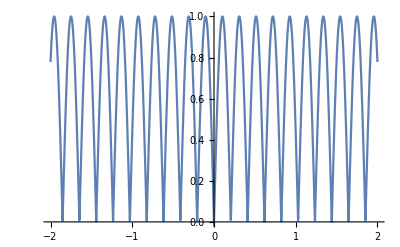

```mathematica
Test1[r_] := π/2-ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])];
Plot[{Test1[r[λ]]},{λ,-2,2}]
Test2[r_] :=(2 Sqrt[A B]Sqrt[(e-r)(r-b)])/(B(e-r)+A(r-b));
Plot[{Test2[r[λ]]},{λ,-2,2}]
```

```mathematica
Test1[r[0.000000001]]
```

1.41581×10^-8

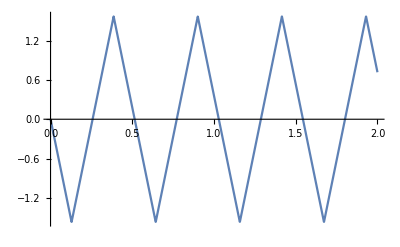

General::ivar: 0.014612 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Test2[r_] :=ArcSin[-((b-e) JacobiSN[√(A B J) λ,k^2] (4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))/(√((A+B+(A-B) JacobiCN[√(A B J) λ,k^2])^2)(b-e) (A+B+(-A+B) JacobiCN[√(A B J) λ,k^2]))]
Plot[Test2[r[λ]],{λ,0,2}]
```

```mathematica
Together[(B(e-(((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)))-A((((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))-b))/(2 Sqrt[A B]Sqrt[(e-(((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)))((((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))-b)])]
```

```mathematica
FullSimplify[(A^2 b B-A b B^2-A^2 B e+A B^2 e-A^2 b B JacobiCN[√(A B J) λ,k^2]-A b B^2 JacobiCN[√(A B J) λ,k^2]+A^2 B e JacobiCN[√(A B J) λ,k^2]+A B^2 e JacobiCN[√(A B J) λ,k^2]-A^2 b B JacobiSN[√(A B J) λ,k^2]^2+A b B^2 JacobiSN[√(A B J) λ,k^2]^2+A^2 B e JacobiSN[√(A B J) λ,k^2]^2-A B^2 e JacobiSN[√(A B J) λ,k^2]^2)/(√(A B) (4 A B+A^2 JacobiSN[√(A B J) λ,k^2]^2-2 A B JacobiSN[√(A B J) λ,k^2]^2+B^2 JacobiSN[√(A B J) λ,k^2]^2) √((e-(2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2])+(A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2)/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)) (-b+(2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2])+(A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2)/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))))]
```

(√(A B) (b-e) JacobiCN[√(A B J) λ,k^2] (-A-B+(A-B) JacobiCN[√(A B J) λ,k^2]))/(√(-(A B (b-e)^2 (-1+JacobiCN[√(A B J) λ,k^2]^2))/((A+B+(A-B) JacobiCN[√(A B J) λ,k^2])^2)) (4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))

```mathematica
ArcSin[(2 Sqrt[A B]Sqrt[(e-r)(r-b)])/(B(e-r)+A(r-b))]
```

```mathematica
ArcSin[-(√(-(A B (b-e)^2 (-1+JacobiCN[√(A B J) λ,k^2]^2))/((A+B+(A-B) JacobiCN[√(A B J) λ,k^2])^2)) (4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))/(√(A B) (b-e) (A+B+(-A+B) JacobiCN[√(A B J) λ,k^2]))]
```

```mathematica
FullSimplify[Together[1/(B(e-(((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)))+A((((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))-b))2 Sqrt[A B]Sqrt[(e-(((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)))((((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))-b)]]]
```

-(√(-(A B (b-e)^2 (-1+JacobiCN[√(A B J) λ,k^2]^2))/((A+B+(A-B) JacobiCN[√(A B J) λ,k^2])^2)) (4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))/(√(A B) (b-e) (A+B+(-A+B) JacobiCN[√(A B J) λ,k^2]))

```mathematica
Test2[r_] :=(2 Sqrt[A B]Sqrt[(e-r)(r-b)])/(B(e-r)+A(r-b));
Plot[{Test2[r[λ]]},{λ,-2,2}]
```

```mathematica
((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)
```

```mathematica
FullSimplify[Together[1/(B(e-(((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)))+A((((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))-b))2 Sqrt[A B]Sqrt[(e-(((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)))((((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))-b)]]]
```

-(√(-(A B (b-e)^2 (-1+JacobiCN[√(A B J) λ,k^2]^2))/((A+B+(A-B) JacobiCN[√(A B J) λ,k^2])^2)) (4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))/(√(A B) (b-e) (A+B+(-A+B) JacobiCN[√(A B J) λ,k^2]))

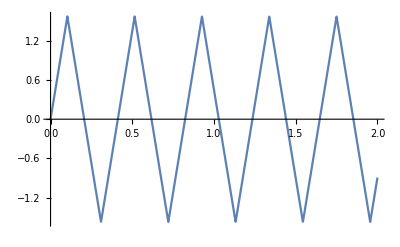

```mathematica
Plot[ArcSin[(JacobiSN[√(A B J) λ,k^2] (4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))/((A+B)^2-(A-B)^2 JacobiCN[√(A B J) λ,k^2]^2)],{λ,0,2}]
```

```mathematica
Plot[JacobiAmplitude'[√(A B J) λ,k^2],{λ,0,2}]
```

-Graphics-

```mathematica
Test1[λ_]:=ArcSin[(JacobiSN[√(A B J) λ,k^2] (4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))/((A+B)^2-(A-B)^2 JacobiCN[√(A B J) λ,k^2]^2)]
Test1[0.0000000000000001]
```

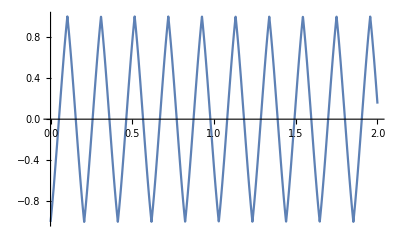

```mathematica
Plot[xSUB[r[λ]]- Cos[ArcSin[ xSUB[r[λ]]]],{λ,0,2}]
```

```mathematica
FullSimplify[(A+B+(A-B) JacobiCN[√(A B J) λ,k^2])^2 (A+B-(A-B) JacobiCN[√(A B J) λ,k^2])^2]
```

```mathematica
((A+B)^2-(A-B)^2 JacobiCN[√(A B J) λ,k^2]^2)
```

```mathematica
FullSimplify[(JacobiSN[√(A B J) λ,k^2] (4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))/((A+B)^2-(A-B)^2 JacobiCN[√(A B J) λ,k^2]^2)]
```

JacobiSN[√(A B J) λ,k^2]

```mathematica
JacobiAmplitude[√(A B J) λ,k^2]
JacobiCN[√(A B J) λ,k^2]
```

```mathematica
Simplify[EllipticPi[-1/f,JacobiAmplitude[√(A B J) λ,k^2],k^2]]
```

EllipticPi[-1/f,JacobiAmplitude[√(A B J) λ,k^2],k^2]

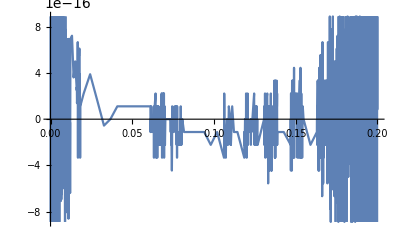

```mathematica
Plot[xSUB[r[λ]]-JacobiSN[√(A B J) λ,k^2],{λ,0,0.2}]
```

```mathematica
FullSimplify[EllipticE[JacobiSN[√(A B J) λ,k^2],k^2]]
```

EllipticE[JacobiSN[√(A B J) λ,k^2],k^2]

```mathematica
FullSimplify[Together[((A (-b+(((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)))-B( e-(((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2))))/(A (b-(((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)))+B (-e+(((A-B) (A b-B e) JacobiSN[√(A B J) λ,k^2]^2+2 (A B (b+e)+A B (b-e) JacobiCN[√(A B J) λ,k^2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,k^2]^2)))))]]
```

JacobiCN[√(A B J) λ,k^2]

```mathematica
T1[λ_] := ((A (-b+r[λ])+B(-e+r[λ]))/(A (b-r[λ])+B (-e+r[λ])))  -CNR[λ]
T2[λ_] :=  xSUB[r[λ]]  - SNR[λ]
T3[λ_] :=√(1-k^2 ( SNR[λ])^2) - DNR[λ]

T4[λ_]:= EllipticF[(π/2 -ArcTan[(B(e-r[λ])-A(r[λ]-b))/(2 Sqrt[A B]Sqrt[(e-r[λ])(r[λ]-b)])]),k^2]- Sqrt[J A B ]λ
```

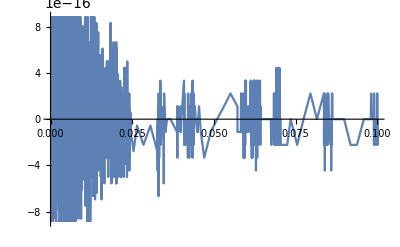

```mathematica
Plot[{T3[λ]},{λ,0,0.1}]
```

```mathematica
T3[0.2`50]
```

0.

```mathematica
FullSimplify[Together[(f k^2+(SNR[λ]) (k^2 SNR[λ]+I k  DNR[λ]))/(√f k √(1+f k^2))]]
```

(ⅈ JacobiDN[√(A B J) λ,k^2] JacobiSN[√(A B J) λ,k^2]+k (f+JacobiSN[√(A B J) λ,k^2]^2))/(√f √(1+f k^2))

```mathematica
FullSimplify[ArcTan[(ⅈ DNR[λ] SNR[λ]+k (f+SNR[λ]^2))/(√f √(1+f k^2))]]
```

ArcTan[(ⅈ JacobiDN[√(A B J) λ,k^2] JacobiSN[√(A B J) λ,k^2]+k (f+JacobiSN[√(A B J) λ,k^2]^2))/(√f √(1+f k^2))]

```mathematica
FullSimplify[EllipticE[AMR[λ],k^2]]
```

EllipticE[JacobiAmplitude[√(A B J) λ,k^2],k^2]

```mathematica
1/((D1M^2-D2M^2) k)√(-k^2) (ArcTanh[(D1M^2 k^2-(SNR[λ]) (k^2 (SNR[λ])+√(-k^2) DNR[λ]))/(D1M k √(-1+D1M^2 k^2))]/(D1M √(-1+D1M^2 k^2))-ArcTanh[(D2M^2 k^2-(SNR[λ]) (k^2 (SNR[λ])+√(-k^2) DNR[λ]))/(D2M k √(-1+D2M^2 k^2))]/(D2M √(-1+D2M^2 k^2)))
```

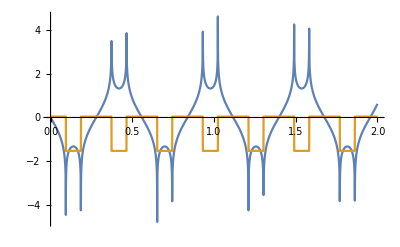

```mathematica
BASETEST[λ_]:= ArcTanh[(k(D1M^2 -  SNR[λ]^2)+I SNR[λ] DNR[λ])/(I D1M  √(1-D1M^2 k^2))]
Test1[λ_]:=-I ArcTan[(k( D1M^2 - SNR[λ]^2)+ I SNR[λ] DNR[λ])/(D1M  √(1-D1M^2 k^2))]
Plot[{Re[Test1[λ]],Im[Test1[λ]]},{λ,0,2}]
Plot[{Re[Test1[λ]]-Re[BASETEST[λ]]},{λ,0,2}]
```

```mathematica
(k( D1M^2 - SNR[λ]^2)+ I SNR[λ] DNR[λ])^2 + ( D1M  √(1-D1M^2 k^2))^2
```

```mathematica
Expand[D1M^2 (1-D1M^2 k^2)+(ⅈ JacobiDN[√(A B J) λ,k^2] JacobiSN[√(A B J) λ,k^2]+k (D1M^2-JacobiSN[√(A B J) λ,k^2]^2))^2]
```

D1M^2+2 ⅈ D1M^2 k JacobiDN[√(A B J) λ,k^2] JacobiSN[√(A B J) λ,k^2]-2 D1M^2 k^2 JacobiSN[√(A B J) λ,k^2]^2-JacobiDN[√(A B J) λ,k^2]^2 JacobiSN[√(A B J) λ,k^2]^2-2 ⅈ k JacobiDN[√(A B J) λ,k^2] JacobiSN[√(A B J) λ,k^2]^3+k^2 JacobiSN[√(A B J) λ,k^2]^4

√(D1M^2+JacobiSN[√(A B J) λ,k^2] (-ⅈ JacobiDN[√(A B J) λ,k^2]+k JacobiSN[√(A B J) λ,k^2]) (-ⅈ JacobiDN[√(A B J) λ,k^2] JacobiSN[√(A B J) λ,k^2]+k (-2 D1M^2+JacobiSN[√(A B J) λ,k^2]^2)))

0.7554903696582065752015861104951233892986244728

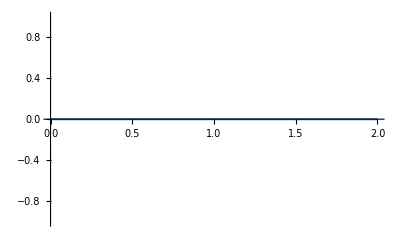

```mathematica
D1M^2
```

```mathematica
Simplify[ ArcTanh[(k(D1M^2 -  SNR[λ]^2)+I SNR[λ] DNR[λ])/(I D1M  √(1-D1M^2 k^2))]]
```

-ⅈ ArcTan[(ⅈ JacobiDN[√(A B J) λ,k^2] JacobiSN[√(A B J) λ,k^2]+k (D1M^2-JacobiSN[√(A B J) λ,k^2]^2))/(D1M √(1-D1M^2 k^2))]

```mathematica
p2 = b*A^2+e*B^2-(e+b)*A*B;
ϡP =(p2-(A-B)^2 RP)^2 
ϛP = 4 A B (A^2 RP (-b-e+2 RP)+(b+e-2 RP) (p2-B^2 RP)+A B ((b-e)^2+2 (b+e) RP-4 RP^2));
ϟP =16 A^2 B^2 (-b+RP) (-e+RP);
βP = -(-2 A b (A-B)^2 B-2 A (A-B)^2 B e+4 A^3 B RP+4 A (A-B)^2 B RP-8 A^2 B^2 RP+4 A B (-p2+B^2 RP));

k = Sqrt[((e-b)^2-(A-B)^2)/(4*A*B)];
```

(A^2 b+B^2 e-A B (b+e)-(A-B)^2 RP)^2

```mathematica
Solve[ϡP λ^2+ϛP λ +ϟP==0,λ]
```

{{λ→-(4 A B)/(A-B)^2},{λ→(4 A B (b-RP) (-e+RP))/(A b-B e-A RP+B RP)^2}}

```mathematica
D1M=Sqrt[ -f]
D2M=Sqrt[(4 A B (RP-b) (e-RP))/(A( b-RP)-B( e- RP))^2]
```

√-f

```mathematica
Apart[1/((λ^2-D1M)(λ^2-D2M))]
```

1/((D1M-D2M) (-D1M+λ^2))+1/((-D1M+D2M) (-D2M+λ^2))

```mathematica
Integrate[-(k^4 √(1-k^2 λ^2))/(2 (-1+D1M k^2) (-1+D2M k^2) (-1+k λ))+(k^4 √(1-k^2 λ^2))/(2 (-1+D1M k^2) (-1+D2M k^2) (1+k λ))-(√(1-k^2 λ^2))/((D1M-D2M) (-1+D1M k^2) (-D1M+λ^2))+(√(1-k^2 λ^2))/((D1M-D2M) (-1+D2M k^2) (-D2M+λ^2)),λ]
```

-(√(-k^2) (-ArcTanh[(D1M k^2-λ (k^2 λ+√(-k^2) √(1-k^2 λ^2)))/(√D1M k √(-1+D1M k^2))]/(√D1M √(-1+D1M k^2))+ArcTanh[(D2M k^2-λ (k^2 λ+√(-k^2) √(1-k^2 λ^2)))/(√D2M k √(-1+D2M k^2))]/(√D2M √(-1+D2M k^2))))/((D1M-D2M) k)

```mathematica
FullSimplify[-(2 D2M (1-D2M^2 k^2) ArcTanh[(I λ)/(√f)]+I √f (2 (-1+D1M^2 k^2) ArcTanh[λ/D2M]-(f+D2M^2) D2M k^3 (Log[1-k λ]-Log[1+k λ])))/(2 I √f (D1M^2-D2M^2) D2M (-1+D1M^2 k^2) (-1+D2M^2 k^2))]
```

```mathematica
(D2M (1-D2M^2 k^2) ArcTan[λ/(√f)]+√f ((-1+D1M^2 k^2) ArcTanh[λ/D2M]+D2M (D2M^2+f) k^3 ArcTanh[k λ]))/(D2M (-D1M^2+D2M^2) √f (1-D1M^2 k^2) (1-D2M^2 k^2))
```

```mathematica
Simplify[ ArcTanh[(k(D1M^2 -  SNR[λ]^2)+I SNR[λ] DNR[λ])/(I D1M  √(1-D1M^2 k^2))]]
```

-ⅈ ArcTan[(ⅈ JacobiDN[√(A B J) λ,(-(A-B)^2+(b-e)^2)/(4 A B)] JacobiSN[√(A B J) λ,(-(A-B)^2+(b-e)^2)/(4 A B)]+1/2 √((-(A-B)^2+(b-e)^2)/(A B)) (-f-JacobiSN[√(A B J) λ,(-(A-B)^2+(b-e)^2)/(4 A B)]^2))/(√-f √(1+((-(A-B)^2+(b-e)^2) f)/(4 A B)))]

```mathematica
HH[λ_]:= (√(-k^2) (ArcTanh[(D1M^2 k^2-λ (k^2 λ+√(-k^2) √(1-k^2 λ^2)))/(D1M k √(-1+D1M^2 k^2))]/(D1M √(-1+D1M^2 k^2))-ArcTanh[(D2M^2 k^2-λ (k^2 λ+√(-k^2) √(1-k^2 λ^2)))/(D2M k √(-1+D2M^2 k^2))]/(D2M √(-1+D2M^2 k^2))))/((D1M^2-D2M^2) k) - (D2M (1-D2M^2 k^2) ArcTan[λ/(√f)]+√f ((-1+D1M^2 k^2) ArcTanh[λ/D2M]+D2M (D2M^2+f) k^3 ArcTanh[k λ]))/(D2M (D2M^2+f) √f (1-D1M^2 k^2) (1-D2M^2 k^2))
```

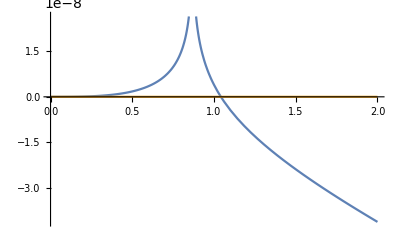

```mathematica
Plot[{Re[HH[λ]],Im[Re[HH[λ]]]},{λ,0,2}]
```

```mathematica
p2 = b*A^2+e*B^2-(e+b)*A*B;
ϡP =(p2-(A-B)^2 RP)^2 ;
ϛP = 4 A B (A^2 RP (-b-e+2 RP)+(b+e-2 RP) (p2-B^2 RP)+A B ((b-e)^2+2 (b+e) RP-4 RP^2));
ϟP =16 A^2 B^2 (-b+RP) (-e+RP);
βP = -(-2 A b (A-B)^2 B-2 A (A-B)^2 B e+4 A^3 B RP+4 A (A-B)^2 B RP-8 A^2 B^2 RP+4 A B (-p2+B^2 RP));
αP =-(A^2 (A-B)^2 RP-2 A (A-B)^2 B RP+(A-B)^2 (-p2+B^2 RP)) ;
k = Sqrt[((e-b)^2-(A-B)^2)/(4*A*B)];
ϡP =(p2-(A-B)^2 RP)^2 ;
f = (4 A B)/(A-B)^2;
ϛP = 4 A B (A^2 RP (-b-e+2 RP)+(b+e-2 RP) (p2-B^2 RP)+A B ((b-e)^2+2 (b+e) RP-4 RP^2));
ϟP =16 A^2 B^2 (-b+RP) (-e+RP);
αP =-(A^2 (A-B)^2 RP-2 A (A-B)^2 B RP+(A-B)^2 (-p2+B^2 RP)) ;
βP = -(-2 A b (A-B)^2 B-2 A (A-B)^2 B e+4 A^3 B RP+4 A (A-B)^2 B RP-8 A^2 B^2 RP+4 A B (-p2+B^2 RP));
γP= -(2 A b (A-B)^2 B-2 A (A-B)^2 B  e);
φP = 8 A^2 b B^2+8 A^2 B^2 e-16 A^2 B^2 RP;
ωP = -8 A^2 b B^2 +8 A^2 B^2 e;
D1P=Sqrt[ -f];
D2P=Sqrt[(4 A B (RP-b) (e-RP))/(A( b-RP)-B( e- RP))^2];
```

```mathematica
FullSimplify[( D2P^2  γP+ωP)/(D2P √(-1+D2P^2 k^2)(D1P-D2P) (D1P+D2P))]
```

```mathematica
(A (A-B)^2 B (b-e)(A (b-RP)+B (-e+RP))^2)/(√(A B (b-RP) (-e+RP)) √((e-b) (A^2 (b-RP)+(e-RP) (b^2-B^2+e RP-b (e+RP)))))
```

```mathematica
FullSimplify[1/(ϡP Sqrt[J A B])I((A (A-B)^2 B (b-e)(A (b-RP)+B (-e+RP))^2)/(√(A B (b-RP) (-e+RP)) √((e-b) (A^2 (b-RP)+(e-RP) (b^2-B^2+e RP-b (e+RP))))))]
```

(ⅈ A B (b-e))/(√(A B J) √(A B (b-RP) (-e+RP)) √((-b+e) (A^2 (b-RP)+(e-RP) (b^2-B^2+e RP-b (e+RP)))))

```mathematica
Þ = Evaluate[4A B( p2(b+e) -A B (b-e)^2)];
ð = Evaluate[8 A^2 B^2(b^2+e^2)];
χ = Evaluate[8 A^2 B^2(b^2-e^2)] ;
ψ = Evaluate[4 A B (b-e) p2];
f = (4 A B)/(A-B)^2;

p2 = b*A^2+e*B^2-(e+b)*A*B;
```

```mathematica
FullSimplify[f √(1+f k^2) p2 √(A B J)]
```

```mathematica
Simplify[(ϵ(RM^2+a^2)-a*L)/(RM-RP)(-((b-e) (A (b-RM)+B (e-RM)))/(2 √(A B J) (b-RM) (-e+RM) (A (b-RM)+B (-e+RM))))+ (ϵ(RP^2+a^2)-a*L)/(RP-RM)(-((b-e) (A (b-RP)+B (e-RP)))/(2 √(A B J) (b-RP) (-e+RP) (A (b-RP)+B (-e+RP))))]
```

((b-e) (-((A (b-RM)+B (e-RM)) (-a L+(a^2+RM^2) ϵ))/((b-RM) (-e+RM) (A (b-RM)+B (-e+RM)) (RM-RP))-((A (b-RP)+B (e-RP)) (-a L+(a^2+RP^2) ϵ))/((b-RP) (-e+RP) (-RM+RP) (A (b-RP)+B (-e+RP)))))/(2 √(A B J))